# IBMRxn

Access the IBM Rxn for Chemistry API with increased functionality.

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
(* Initial run of this notebook will prompt you to enter your authorization key. Once you've done that feel free to delete the following cell. *)
```

```mathematica
SystemCredential["authKey"]=InputString["Authorization Key"];
```

```mathematica
authKey=SystemCredential["authKey"];
```

```mathematica
baseURL="rxn.res.ibm.com";
```

```mathematica
reacSplit[reacs_String]:=StringSplit[reacs,">>"];
```

```mathematica
IBMRxn[req_String,molecs_List,projID_String]:=Module[
{reactantList={},createProj,projectID,createPred,getPred,rxnImg,rxnConf,predID,projName,reactants},

If[(* If[] you want to make a "new prediction", this code block runs *)
req=="new prediction",
Do[
Which[
ImageQ[molecs[[i]]],
AppendTo[reactantList,MoleculeRecognize[molecs[[i]]]["SMILES"]]
,
StringQ[molecs[[i]]],
AppendTo[reactantList,molecs[[i]]]
],{i,1,Length[molecs]}];

reactants=ToString[Row[#,"."]&@reactantList];
createPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/pr?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
predID=createPred["payload","id"];

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projectID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
]]
```

```mathematica
(* duplicate of above - for adding a output format parameter *)
```

```mathematica
rxn[req_String,molecs_List,projID_String,outType_String]:=Module[
{reactantList={},createProj,projectID,createPred,getPred,rxnImg,rxnConf,predID,projName,reactants,rsmiles},

If[(* If[] you want to make a "new prediction", this code block runs *)
req=="new prediction",
Do[
Which[
ImageQ[molecs[[i]]],
AppendTo[reactantList,MoleculeRecognize[molecs[[i]]]["SMILES"]]
,
StringQ[molecs[[i]]],
AppendTo[reactantList,molecs[[i]]]
],{i,1,Length[molecs]}];

reactants=ToString[Row[#,"."]&@reactantList];
createPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/pr?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
predID=createPred["payload","id"];

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

Which[
outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projectID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];
rsmiles=getPred["payload","attempts"][[1]]["smiles"];

<|"project name"->projName,"projID"->projectID,"predID"->predID,"rreac"->reacSplit[rsmiles][[1]],"rprod"->reacSplit[rsmiles][[2]],"conf"->rxnConf,"reaction image"->rxnImg|>//Dataset
]
]]
```

```mathematica
(* for getting more outcomes from a prediction that you've already made *)
```

```mathematica
IBMRxn[req_String,projID_String,predID_String]:=Module[
{getPred,reactants,morePreds,projName,rxnImgList={},rxnConfList={},rxnImages,rxnTables,preds},

If[req=="more predictions",
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
reactants=getPred["payload","request","reactants"];

Pause[10];

morePreds=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/prb?predictionId="<>predID<>"&projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];


rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;
rxnTables=TableForm[{{projName,projID,predID,#}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]&/@rxnConfList;

preds=Partition[Riffle[rxnImages,rxnTables],2];
preds
]]
```

```mathematica
(* duplicate of above - for adding an output type *)
```

```mathematica
IBMRxn[req_String,projID_String,predID_String,outType_String]:=Module[
{getPred,reactants,morePreds,projName,rxnImgList={},rxnConfList={},rsmilesList={},rxnImages,rxnTables,preds},

If[req=="more predictions",
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
reactants=getPred["payload","request","reactants"];

Pause[10];

morePreds=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/prb?predictionId="<>predID<>"&projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

Which[
outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];


rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;
rxnTables=TableForm[{{projName,projID,predID,#}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]&/@rxnConfList;

preds=Partition[Riffle[rxnImages,rxnTables],2];
preds
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
	Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each rsmiles to the list *)
AppendTo[rsmilesList,getPred["payload","attempts"][[i]]["smiles"]],
{i,1,Length[getPred["payload","attempts"]]}];

rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;

Dataset@MapThread[<|"project name"->projName,"projID"->projID,"predID"->predID,"rreac"->reacSplit[#1][[1]],"rprod"->reacSplit[#1][[2]],"conf"->#2,"reaction image"->#3|>&,{rsmilesList,rxnConfList,rxnImages}]
]
]]
```

```mathematica
(* for making a new retrosynthesis *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100]},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->"",
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];

retImg
retTable
]]
```

```mathematica
(* duplicate of above - added to specify a precursor *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List,prec_String]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],out,seqs,childsNumb,cImgs,childs,product},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->prec,
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];*)

seqs=Length@getRet["payload","sequences"];

retImg=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{product,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]

(*retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];*)
]]
```

```mathematica
(* duplicate of above - added to specify output type *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List,prec_String,outType_String]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],out,seqs,childsNumb,cImgs,childs,product,cols,cSMILES,retroID},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->prec,
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];*)

Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

retImg=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{product,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

cols=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"];
retroID=getRet["payload","sequences"][[1]]["retrosynthesisId"];
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cSMILES=Flatten@Rest@out;

{rClass,projID,retroID,cSMILES,product,retConf,retOptScore}
,{i,1,seqs}];
MapThread[<|"rclass"->#1,"projID"->#2,"retroID"->#3,"rreac"->StringRiffle[#4,"."],"prod"->#5,"conf"->#6,"opt"->#7|>&,{cols[[All,1]],cols[[All,2]],cols[[All,3]],cols[[All,4]],cols[[All,5]],cols[[All,6]],cols[[All,7]]}]//Dataset
]

(*retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];*)
]]
```

```mathematica
(* for making a new project, listing all project attempts, or recovering a past prediction or retrosynthesis *)
```

```mathematica
IBMRxn[req_String,IDorName_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,allProjAs,getPred,projName,rxnImg,rxnConf,predID,projID,createProj,projectID,getRet,seqMolecList,seqSMILES,retConf,retOptScore,molecPlots,retTable,stepsImgs,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],stepDescs,retImg,prodSMILES,rClass,seqConf,seqs,prod,childsNumb,out,cImgs,childs},

Which[
req=="new project",(* for a "new project", following code block runs *)
createProj=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"name"->ToString[IDorName],"invitations"->{}|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
projectID=createProj["payload","id"];
TableForm[{{IDorName,projectID}},TableHeadings->{None,{"Project Name","Project ID"}}]
,
req== "all project attempts",(* for getting "all project attempts", following code block runs *)
allProjAs=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects/"<>IDorName<>"/attempts?raw={}"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
allProjAs,
req=="recover prediction",(* to "recover prediction", following code block runs *)
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
req=="recover retrosynthesis",(* recover a previously made retrosynthesis *)
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

While[
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
projID=getRet["payload","projectId"];

(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

prodSMILES=getRet["payload","wizardParameters","exclude_smiles"][[1]];
molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];

retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)

seqs=Length@getRet["payload","sequences"];

retImg=Table[
prod=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{prod,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,IDorName,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]

(*retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)
]]
```

```mathematica
(* duplicate of above - added to allow for specifying ouput type *)
```

```mathematica
IBMRxn[req_String,IDorName_String,outType_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,allProjAs,getPred,projName,rxnImg,rxnConf,predID,projID,createProj,projectID,getRet,seqMolecList,seqSMILES,retConf,retOptScore,molecPlots,retTable,stepsImgs,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],stepDescs,retImg,prodSMILES,rClass,seqConf,seqs,prod,childsNumb,out,cImgs,childs,retroID,product,cols,cSMILES,rsmiles},

Which[
req=="new project",(* for a "new project", following code block runs *)
createProj=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"name"->ToString[IDorName],"invitations"->{}|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
projectID=createProj["payload","id"];
TableForm[{{IDorName,projectID}},TableHeadings->{None,{"Project Name","Project ID"}}]
,
req== "all project attempts",(* for getting "all project attempts", following code block runs *)
allProjAs=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects/"<>IDorName<>"/attempts?raw={}"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
allProjAs,
req=="recover prediction",(* to "recover prediction", following code block runs *)
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];
rsmiles=getPred["payload","attempts"][[1]]["smiles"];

<|"project name"->projName,"projID"->projID,"predID"->predID,"rreac"->reacSplit[rsmiles][[1]],"rprod"->reacSplit[rsmiles][[2]],"conf"->rxnConf,"reaction image"->rxnImg|>//Dataset
]
,
req=="recover retrosynthesis",(* recover a previously made retrosynthesis *)
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

While[
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
projID=getRet["payload","projectId"];

(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

prodSMILES=getRet["payload","wizardParameters","exclude_smiles"][[1]];
molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];

retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)

Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

retImg=Table[
prod=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{prod,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,IDorName,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

cols=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"];
retroID=getRet["payload","sequences"][[1]]["retrosynthesisId"];
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cSMILES=Flatten@Rest@out;

{rClass,projID,retroID,cSMILES,product,retConf,retOptScore}
,{i,1,seqs}];
MapThread[<|"rclass"->#1,"projID"->#2,"retroID"->#3,"rreac"->StringRiffle[#4,"."],"prod"->#5,"conf"->#6,"opt"->#7|>&,{cols[[All,1]],cols[[All,2]],cols[[All,3]],cols[[All,4]],cols[[All,5]],cols[[All,6]],cols[[All,7]]}]//Dataset
]

(*retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)
]]
```

```mathematica
(* just for getting all stored projects. if "stored projects" is given as input, outputs a dataset of all stored projects as well as the total number of projects stored *)
```

```mathematica
IBMRxn[req_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,queueState},
Which[(* If[] you want to get all "stored projects", this code block runs *)
req=="stored projects",
myProjects=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;

myProjNames=#["name"]&/@myProjects["payload","content"];
myProjIDs=#["id"]&/@myProjects["payload","content"];

nameRule=("Project Name"->#&/@myProjNames);
idRule=("Project ID"->#&/@myProjIDs);

myProjectsData=
Dataset[
Association[#]&/@Transpose[{nameRule,idRule}]]
TableForm[{{ToString[myProjects["payload","totalElements"]]}},TableHeadings->{None,{"Total Stored Projects"}},TableAlignments->Center]
,
req=="queue status",(* get the status of the retrosynthesis queue *)
queueState=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/queue-state"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;

queueState
]]
```

```mathematica
reacSplit[reacs_String]:=StringSplit[reacs,">>"];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

IBMRxn["new project",projectName_Str]

creates a new project with name projectName and returns projectName and the project ID.

IBMRxn["new prediction",{reactants_Str/Img}, projectID_Str]

creates a new forward reaction prediction in the project corresponding to projectID using the supplied reactants.

IBMRxn["new retrosynthesis",projectID_str,{product molecule_Str/Img}]

creates a new retrosynthetic prediction in the project corresponding to projectID using the supplied product molecule.

IBMRxn["more predictions",projectID_Str, predictionID_Str]

Gets all of the predictions corresponding to predictionID in the project corresponding to projectID.

IBMRxn["recover prediction",predictionID_Str]

recovers the prediction corresponding to predictionID.

IBMRxn["recover retrosynthesis",retrosynthesisID_Str]

recovers the retrosynthesis corresponding to retrosynthesisID.

IBMRxn["stored projects"]

gets a dataset of all of the stored projects corresponding to the apk-key

IBMRxn["all project attempts",projectID_Str]

gets all of the attempts in the project corresponding to projectID.

IBMRxn["queue status"]

gets the current status of the API queue.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

new prediction, new retrosynthesis, more predictions, recover prediction, and recover retrosynthesis take the additonal option output Type:

Output Types | Output Format
default/"" | Reaction image and prediction/retrosynthesis information table
dataset | Dataset of SMILES, reaction type, and prediction/retrosynthesis information. Includes a reaction image in the case of a prediction.

new retrosynthesis takes the additional option precursors before output Type, which can specify specific precursor molecule(s) to use for starting the retrosynthesis

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Create a new project:

```mathematica
IBMRxn["new project","myProject"]
```

Project Name | Project ID
myProject | 5f3826f45ce6d30001718309

Create a new prediction and output a reaction image and prediction information table:

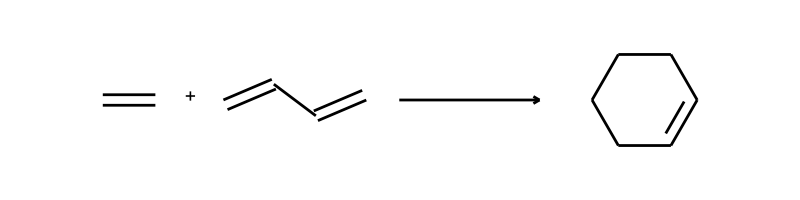
-Graphics- Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5f3826f45ce6d30001718309 | 5f38280d5ce6d3000171833d | 0.208485

```mathematica
IBMRxn["new prediction",{Molecule["ethene"]["CanonicalSMILES"],Molecule["butadiene"]["CanonicalSMILES"]},"5f3826f45ce6d30001718309"]
```

Get all of the forward predictions for a previous prediction in dataset form:

```mathematica
IBMRxn["more predictions","5f3826f45ce6d30001718309","5f38280d5ce6d3000171833d","dataset"]
```

Create a new retrosynthesis and output a dataset:

```mathematica
IBMRxn["new retrosynthesis","5f3826f45ce6d30001718309",{Molecule["1,3-dibromobenzene"]["CanonicalSMILES"]},"","dataset"]
```

View all of your stored projects:

```mathematica
IBMRxn["stored projects"]
```

Total Stored Projects
28

### Scope

IBMRxn takes advantage of Mathematica's MoleculeRecognize functionality to allow for molecule images to be provided as input:

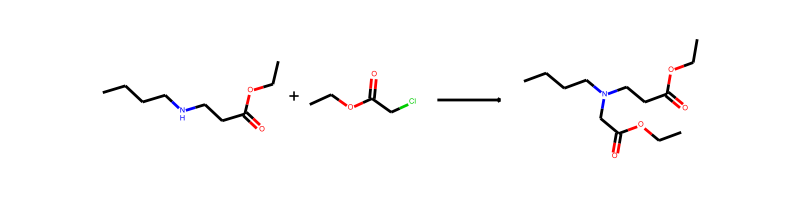
-Graphics- Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5f3826f45ce6d30001718309 | 5f382ad15ce6d30001718418 | 0.883702

```mathematica
IBMRxn["new prediction",{-Graphics-,-Graphics-},"5f3826f45ce6d30001718309"]
```

You can supply a mixture of images and strings and IBMRxn will parse them separately:

```mathematica
IBMRxn["new prediction",{-Graphics-,"CCOC(=O)CCl"},"5f3826f45ce6d30001718309"]
```

-Graphics- Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5f3826f45ce6d30001718309 | 5f382b315ce6d30001718434 | 0.883702

### Options

Output type allows you to get output as a default image and table or as a dataset, allowing for further processing:

```mathematica
IBMRxn["recover prediction","5f382ad15ce6d30001718418","default"]
```

-Graphics- Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5f3826f45ce6d30001718309 | 5f382ad15ce6d30001718418 | 0.883702

```mathematica
(* Getting a dataset form can allow further computation with the results *)
```

```mathematica
myRxn=IBMRxn["recover prediction","5f382ad15ce6d30001718418","dataset"];
```

```mathematica
myRxn["reaction image"]
```

-Graphics-

```mathematica
IBMRxn["more predictions",myRxn["projID"],myRxn["predID"],"dataset"]
```

### Applications

### Properties and Relations

### Possible Issues

While the IBMRxn function includes Pauses to prevent too many API requests, if you make too many separate requests in a short period of time you may stop getting output. If this occurs wait a few minutes before making another request.

### Neat Examples

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

William Borrelli <wborrelli@fordham.edu>

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

machine learning

chemistry

cheminformatics

image recognition

API

retrosynthesis

reaction prediction

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

Molecule

MoleculeRecognize

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

SVGImport

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

(1) Schwaller, P.; Laino, T.; Gaudin, T.; Bolgar, P.; Hunter, C. A.; Bekas, C.; Lee, A. A. Molecular Transformer: A Model for Uncertainty-Calibrated Chemical Reaction Prediction. ACS Cent. Sci. 2019, 5 (9), 1572–1583. https://doi.org/10.1021/acscentsci.9b00576.

(2) Schwaller, P.; Petraglia, R.; Zullo, V.; Nair, V. H.; Haeuselmann, R. A.; Pisoni, R.; Bekas, C.; Iuliano, A.; Laino, T. Predicting Retrosynthetic Pathways Using Transformer-Based Models and a Hyper-Graph Exploration Strategy. Chem. Sci. 2020, 11 (12), 3316–3325. https://doi.org/10.1039/C9SC05704H.

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

https://rxn.res.ibm.com/

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

Additional information about limitations, issues, etc.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

You will need to input a/your apk key from your IBM Rxn for Chemistry profile in order for the examples to run. You will also likely need to update the project/prediction/retrosynthesis ID's in each example.